## Introduction

Can we solve swarm robotics using “swarmalator control”?

## Simulations

$Aborted

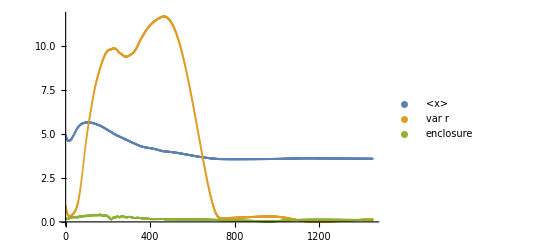

```mathematica
SeedRandom[0];
{dt,T,n}={0.2,2000,50};
L=2;
{J,k,α}={4,0.5,1};
{R,ω}={5,0.005};
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
results={};Dynamic[results]
{t,NT}={0,Round[T/dt]};
scores={};
While[t<NT,
zgoal={R Cos[ω t], R Sin[ω t]};
(*zGoal={0, R Sin[ω t]};
zGoal={0, ω t};*)
(*zgoal={0,0};*)
znew=rk4[z0,zgoal,rhs,dt,J,k,α];
z0=znew;t++;AppendTo[scores,{meanDistance[znew,zgoal],radialVariance[znew,zgoal],occlusionScore[znew,zgoal]}];
results=plotResults[znew,L=5,zGoal=zgoal];
];
ListPlot[{scores[[All,1]],scores[[All,2]],scores[[All,3]]},AxesOrigin->{0,0},PlotLegends->{"<x>","var r", "enclosure"}]
```

### No video

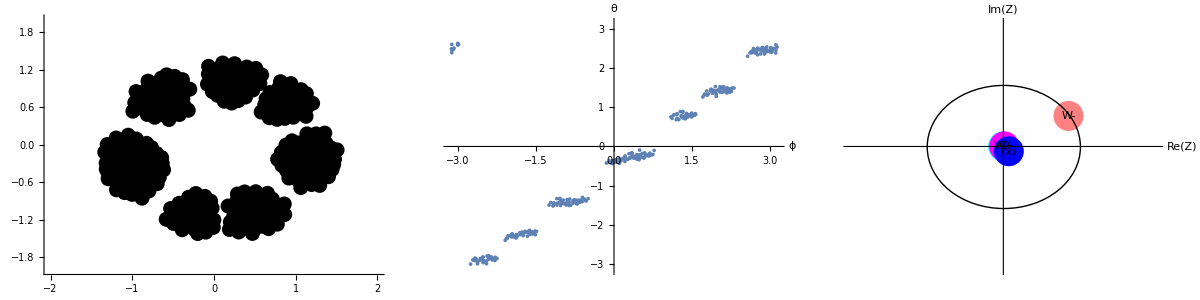

```mathematica
SeedRandom[1];
{dt,T,n}={0.1,5000,300};
{J,k}={1,-0.05};
z0=Table[{RandomReal[{-4,4}],RandomReal[{-4,4}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
results={};Dynamic[results]
{t,NT}={0,Round[T/dt]};
{Z1,sols}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k];
z0=znew;t++;AppendTo[sols,znew];
];
p1=plotResults[znew]
```

## Catalog

### C shape

$Aborted

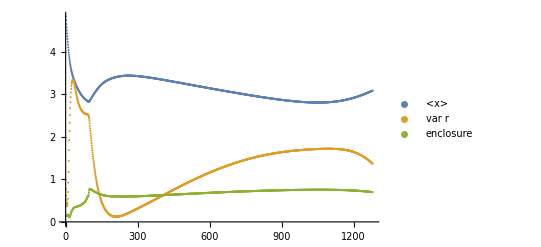

```mathematica
SeedRandom[0];
{dt,T,n}={0.5,2000,50};
L=2;
{J,k,α}={2.5,-2,1.55};
{R,ω}={5,0.005};
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
results1={};Dynamic[results1]
{t,NT}={0,Round[T/dt]};
scores={};
While[t<NT,
zgoal={R Cos[ω t], R Sin[ω t]};
(*zGoal={0, R Sin[ω t]};
zGoal={0, ω t};*)
(*zgoal={0,0};*)
znew=rk4[z0,zgoal,rhs,dt,J,k,α];
z0=znew;t++;AppendTo[scores,{meanDistance[znew,zgoal],radialVariance[znew,zgoal],occlusionScore[znew,zgoal]}];
results1=plotResults[znew,L=10,zGoal=zgoal];
];
ListPlot[{scores[[All,1]],scores[[All,2]],scores[[All,3]]},AxesOrigin->{0,0},PlotLegends->{"<x>","var r", "enclosure"}]
```

### Total circle

$Aborted

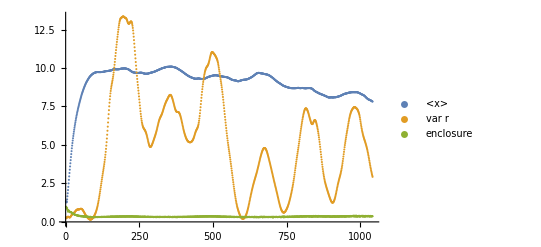

```mathematica
SeedRandom[0];
{dt,T,n}={0.5,2000,50};
L=2;
{J,k,α}={5,-2,1.55};
{R,ω}={5,0.01};
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
results2={};Dynamic[results2]
{t,NT}={0,Round[T/dt]};
scores={};
While[t<NT,
zgoal={R Cos[ω t], R Sin[ω t]};
zgoal={R Sin[ω t],R Sin[2 ω t]};
(*zgoal={0, R Sin[ω t]};*)
(*zGoal={0, ω t};*)
(*zgoal={0,0};*)
znew=rk4[z0,zgoal,rhs,dt,J,k,α];
z0=znew;t++;AppendTo[scores,{meanDistance[znew,zgoal],radialVariance[znew,zgoal],occlusionScore[znew,zgoal]}];
results2=plotResults[znew,L=15,zGoal=zgoal];
];
ListPlot[{scores[[All,1]],scores[[All,2]],scores[[All,3]]},AxesOrigin->{0,0},PlotLegends->{"<x>","var r", "enclosure"}]
```

### Figure of 8

$Aborted

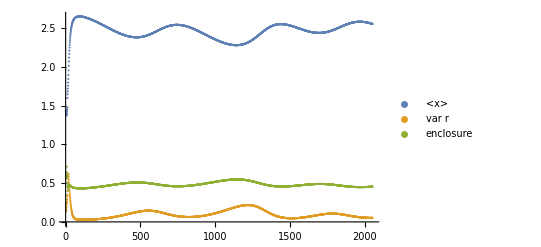

```mathematica
SeedRandom[0];
{dt,T,n}={0.5,2000,20};
L=2;
{J,k,α}={2,-2,1.55};
{R,ω}={5,0.0025};
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
results2={};Dynamic[results2]
{t,NT}={0,Round[T/dt]};
scores={};
While[t<NT,
zgoal={R Cos[ω t], R Sin[ω t]};
zgoal={R Sin[ω t],R Sin[2 ω t]};
(*zgoal={0, R Sin[ω t]};*)
(*zGoal={0, ω t};*)
(*zgoal={0,0};*)
znew=rk4[z0,zgoal,rhs,dt,J,k,α];
z0=znew;t++;AppendTo[scores,{meanDistance[znew,zgoal],radialVariance[znew,zgoal],occlusionScore[znew,zgoal]}];
results2=plotResults[znew,L=15,zGoal=zgoal];
];
ListPlot[{scores[[All,1]],scores[[All,2]],scores[[All,3]]},AxesOrigin->{0,0},PlotLegends->{"<x>","var r", "enclosure"}]
```

```mathematica
SeedRandom[0];
{dt,T,n}={0.5,2000,20};
L=2;
{J,k,α}={2,-2,1.55};
{R,ω}={5,0.0025};
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
results2={};Dynamic[results2]
{t,NT}={0,Round[T/dt]};
scores={};
While[t<NT,
zgoal={R Cos[ω t], R Sin[ω t]};
zgoal={R Sin[ω t],R Sin[2 ω t]};
(*zgoal={0, R Sin[ω t]};*)
(*zGoal={0, ω t};*)
(*zgoal={0,0};*)
znew=rk4[z0,zgoal,rhs,dt,J,k,α];
z0=znew;t++;AppendTo[scores,{meanDistance[znew,zgoal],radialVariance[znew,zgoal],occlusionScore[znew,zgoal]}];
results2=plotResults[znew,L=15,zGoal=zgoal];
];
ListPlot[{scores[[All,1]],scores[[All,2]],scores[[All,3]]},AxesOrigin->{0,0},PlotLegends->{"<x>","var r", "enclosure"}]
```

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{zgoal,_Real,1},{n,_Integer},{J,_Real},{K,_Real},{α,_Real}},
Module[{i,j,xji,yji,thetaji,distSq,xtemp,ytemp,xgoal,ygoal,aGoal,xdistGoal,ydistGoal,distGoal,thetatemp,xRepGoal,kGoal,goalRadius,yRepGoal,parabolicDistCutoff,dist,vel=ConstantArray[0.0,{3,n}]},
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
yji=z[[2,j]]-z[[2,i]];
thetaji=z[[3,j]]-z[[3,i]];
distSq=xji^2+yji^2;
dist=√distSq;
xtemp=xji((1 + J Cos[thetaji])/dist- 1/distSq);
ytemp=yji((1 + J Cos[thetaji])/dist-1/distSq);
thetatemp=K*Sin[thetaji-α] /dist; 
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=ytemp;vel[[2,j]]+=-ytemp;
vel[[3,i]]+=thetatemp;vel[[3,j]]+=-thetatemp;
];

(*Goal term*)
{kGoal,aGoal,goalRadius}={2,10,0.2};
{xgoal,ygoal}=zgoal;
{xdistGoal,ydistGoal}={xgoal-z[[1,i]],ygoal-z[[2,i]]};
distGoal=√(xdistGoal^2+ydistGoal^2);
{xRepGoal,yRepGoal}={If[distGoal<goalRadius,xdistGoal/distGoal^2,0],If[distGoal<goalRadius,ydistGoal/distGoal^2,0]};
{xRepGoal,yRepGoal}={xdistGoal/distGoal^2,ydistGoal/distGoal^2};
vel[[1,i]]+= kGoal xdistGoal-aGoal xRepGoal;
vel[[2,i]]+= kGoal ydistGoal-aGoal yRepGoal;
];
vel/N[n]
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

rhsNavigate=Compile[{{z,_Real,2},{zGoal,_Real,1},{n,_Integer},{J,_Real},{K,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,α1,α,xGoal,yGoal,kGoal,
distSq,dist,xtemp,ytemp,a,thetatemp,xgoal,ygoal,xdistGoal,xRepGoal,yRepGoal,distGoal,ydistGoal,goalRadius,vel=ConstantArray[0.0,{3,n}]},
{a,α1}={0,1.55};
goalRadius=1.0;
kGoal=0;
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
If[i≠j,
xji=z[[1,j]]-z[[1,i]];
yji=z[[2,j]]-z[[2,i]];
thetaji=z[[3,j]]-z[[3,i]];
distSq=xji^2+yji^2;
inverseDistSq=1/distSq;
dist=√distSq;
xtemp=xji((1 + J Cos[thetaji])/dist- 6inverseDistSq);
ytemp=yji((1 + J Cos[thetaji])/dist- 6 inverseDistSq);
thetatemp=K*Sin[thetaji-α1] /dist; 
vel[[1,i]]+=xtemp;
vel[[2,i]]+=ytemp;
vel[[3,i]]+=thetatemp;
];
];

(*Goal term*)
{xgoal,ygoal}=zGoal;
{xdistGoal,ydistGoal}={xgoal-z[[1,i]],ygoal-z[[2,i]]};
distGoal=√(xdistGoal^2+ydistGoal^2);
{xRepGoal,yRepGoal}={If[distGoal<goalRadius,xdistGoal/distGoal^4,0],If[distGoal<goalRadius,ydistGoal/distGoal^4,0]};
vel[[1,i]]+=kGoal xdistGoal-a xRepGoal;
vel[[2,i]]+=kGoal ydistGoal-a yRepGoal;
];
vel/N[n]
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];


rk4[z_,zGoal_,F_,dt_,J_,K_,α_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,zGoal,n,J,K,α];
k2=F[z+dt/2 k1,zGoal,n,J,K,α];
k3=F[z+dt/2 k2,zGoal,n,J,K,α];
k4=F[z+dt k3,zGoal,n,J,K,α];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

plotResults[z_,L_:2,zGoal_:{0,0}]:=Block[{colors,p1,p2,p3,Z,Wp,Wm,meanX,meanY,ϕ,θ},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors],Black,Text[Style["X",25],{zGoal[[1]],zGoal[[2]]}]},
PlotRange->{{-L,L},{-L,L}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{"x"},LabelStyle->15];

ϕ=ArcTan[z[[1,All]],z[[2,All]]];
θ=z[[3,All]];
p2=ListPlot[{ϕ//mod,θ//mod}ᵀ,AxesLabel->{"ϕ","θ"},LabelStyle->15,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium];

{Z,Wp,Wm}=findOrderPars[z];
{meanX,meanY}={Mean[z[[1,All]]],Mean[z[[2,All]]]};
p3=Graphics[{PointSize[0.06],
Cyan,Point[{Z//Re,Z//Im}],Black,Text["Z",{Z//Re,Z//Im}],
Magenta,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Pink,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],
Blue,Point[{meanX,meanY}],Black,Text["⟨x⟩",{meanX,meanY}],
Circle[{0,0},1]
},AxesOrigin->{0,0},PlotRange->{{-L,L},{-L,L}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"Re(Z)","Im(Z)"},LabelStyle->15,ImageSize->Medium];

Return[Grid[{{p1,p2,p3}}]];

];

findOrderPars[z_]:=Block[{Z,Wp,Wm,i,numOsc,ϕ,θ},
{Z,Wp,Wm}={0,0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
{ϕ,θ}={ArcTan[z[[1,i]],z[[2,i]]],z[[3,i]]};
Z+=Exp[ⅈ θ];
Wp+=Exp[ⅈ(ϕ+θ)];
Wm+=Exp[ⅈ(ϕ-θ)];
];
Return[{Z/numOsc,Wp/numOsc,Wm/numOsc}]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

meanDistance[z_,zGoal_]:=Mean[Norm/@Transpose[z[[1;;2]]-zGoal]];

radialVariance[z_,zGoal_]:=Module[{radii},radii=Norm/@Transpose[z[[1;;2]]-zGoal];Variance[radii]];

collisionCount[z_,ϵ_:0.5]:=Module[{positions,n,count=0},positions=Transpose[z[[1;;2]]];(*extract x,y*)
n=Length[positions];
Do[If[Norm[positions[[i]]-positions[[j]]]<ϵ,count++],{i,1,n},{j,i+1,n}];
count];

occlusionScore[z_,zGoal_,agentRadius_:0.2]:=Module[{positions,relativeVecs,angles,deltas,intervals,merged,totalAngle},positions=Transpose[z[[1;;2]]];
relativeVecs=positions-ConstantArray[zGoal,Length[positions]];
angles=ArcTan@@@relativeVecs;
deltas=ArcSin[Clip[agentRadius/Norm/@relativeVecs,{0,1}]];
intervals=Transpose[{angles-deltas,angles+deltas}];
intervals=Mod[#,2 Pi]&/@intervals;
intervals=Flatten[Table[If[int[[1]]>int[[2]],{{int[[1]],2 Pi},{0,int[[2]]}},{int}],{int,intervals}],1];
merged=SortBy[intervals,First];
merged=Fold[Function[{acc,next},If[Last[Last[acc]]≥First[next],ReplacePart[acc,-1->{First[Last[acc]],Max[Last[Last[acc]],Last[next]]}],Append[acc,next]]],{First[merged]},Rest[merged]];
totalAngle=Total[Last[#]-First[#]&/@merged];
totalAngle/(2 Pi)
];
```